# Graphene superlattices:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jass/Downloads

## Twisted double-bilayer graphene:

```mathematica
ColorCarb=Blue;
ColorCarb2=RGBColor[0.31,0.52,1.];
ColorCarb3=Red;
ColorCarb4=RGBColor[1.,0.7,0.6];


aLattice=8.8;
RCarb=1.30/aLattice;
RBonds=0.04;
```

Atom positions and bonds: (Image size 2000)

For graphene nematicity

```mathematica
aLattice=8.8;
RCarb=1.0/aLattice;
RBonds=0.04;
scale1 = 2.4;
scale2 = 0.7;
```

```mathematica
m=29;
r=7;
θ=-(ArcCos[(3 m^2+3m r+r^2/2)/(3 m^2+3m r+r^2)])*1.018;
θ0=30*2π/360;
θ//N;

NAtoms=11;
NAtomsL=11;


Shiftz=0.4;
Shift={-1/√3,0,0};
PositionsCarbon=Join[Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1],Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1]];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

PositionsCarbon2=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,Shiftz}&/@PositionsCarbon;
Bonds21={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds1;
Bonds22={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds2;
Bonds23={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds3;
 
θ=-θ;

PositionsCarbon3=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)+{0,0,2Shiftz}&/@PositionsCarbon;
Bonds31={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds1;
Bonds32={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds2;
Bonds33={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds3;

PositionsCarbon4=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,3Shiftz}&/@PositionsCarbon;
Bonds41={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds1;
Bonds42={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds2;
Bonds43={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds3;
```

```mathematica
FULLLattice=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds*scale1],Cylinder[Bonds12,RBonds*scale2],Cylinder[Bonds13,RBonds*scale2],ColorCarb2,Sphere[PositionsCarbon2,RCarb],Cylinder[Bonds21,RBonds*scale1],Cylinder[Bonds22,RBonds*scale2],Cylinder[Bonds23,RBonds*scale2],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3,RCarb],Cylinder[Bonds31,RBonds*scale1],Cylinder[Bonds32,RBonds*scale2],Cylinder[Bonds33,RBonds*scale2],ColorCarb4,Sphere[PositionsCarbon4,RCarb],Cylinder[Bonds41,RBonds*scale1],Cylinder[Bonds42,RBonds*scale2],Cylinder[Bonds43,RBonds*scale2]},ImageSize->1000,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

## Adding the high-symmetry points:

```mathematica
ColorMoire=Green;
Color2=Gray;
Color3=Gray;
RadiusRegions=1;

MRLength=0.99/(2Sin[θ/2]);
a1=MRLength {Cos[π/6],Sin[π/6],0};
a2=MRLength{Cos[π/6],-Sin[π/6],0};
δ1=(a1+a2)/3;
δ2=2*(a1+a2)/3;

HighSymPts=Graphics3D[Join[{ColorMoire,Opacity[0.2],EdgeForm[None]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}},RadiusRegions],{n,{{0,0},{1,0},{0,1},{-1,0},{0,-1},{1,-1},{-1,1},{-2,0},{2,0}}}],{Color2,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ1,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ1},RadiusRegions],{n,{{0,0},{-1,-1},{-1,0},{-1,1},{0,-1},{1,-1},{1,0},{-2,0}}}],{Color3,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ2},RadiusRegions],{n,{{0,0},{0,-1},{0,-2},{-1,0},{-1,-1},{-2,0},{1,-1},{-2,-1}}}]],ViewPoint->{0,0,Infinity}];
```

```mathematica
Show[FULLLattice,HighSymPts,ImageSize->2000,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Export["disks.svg",%]
```

disks.svg

## A close-up view:

```mathematica
θ0=30*2π/360;
θ=-15.5*2π/360;
θ0=30*2π/360;

NAtoms=2;
NAtomsL=2;


Shiftz=0.4;
Shift={-1/√3,0,0};
PositionsCarbon=Join[Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1],Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1]];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

PositionsCarbon2=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,Shiftz}&/@PositionsCarbon;
Bonds21={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds1;
Bonds22={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds2;
Bonds23={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds3;
 
θ=-θ;

PositionsCarbon3=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)+{0,0,2Shiftz}&/@PositionsCarbon;
Bonds31={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds1;
Bonds32={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds2;
Bonds33={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds3;

PositionsCarbon4=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,3Shiftz}&/@PositionsCarbon;
Bonds41={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds1;
Bonds42={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds2;
Bonds43={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds3;

CloseUpView=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],ColorCarb2,Sphere[PositionsCarbon2,RCarb],Cylinder[Bonds21,RBonds],Cylinder[Bonds22,RBonds],Cylinder[Bonds23,RBonds],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3,RCarb],Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds],ColorCarb4,Sphere[PositionsCarbon4,RCarb],Cylinder[Bonds41,RBonds],Cylinder[Bonds42,RBonds],Cylinder[Bonds43,RBonds]},ImageSize->1000,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
Export["disksCLOSEUP.svg",%]
```

TDBGCloseUp.bmp

## For the BZs I will need once this plot:

Bravais lattice:

```mathematica
a1={Cos[π/6],Sin[π/6]};
a2={Cos[π/6],-Sin[π/6]};
```

Reciprocal lattice vectors:

```mathematica
b1=2π *(RotationMatrix[π/2].a2)/(a1.RotationMatrix[π/2].a2)
b2=2π *(RotationMatrix[π/2].a1)/(a2.RotationMatrix[π/2].a1)
{a1.b1,a2.b2,a1.b2,a2.b1}
```

{(2 π)/(√3),2 π}

{(2 π)/(√3),-2 π}

{2 π,2 π,0,0}

```mathematica
Dir=b1+(b1+b2);
C1=Norm[b1]/(2Cos[π/6])*Dir/Norm[Dir];
Γp={0,0};
Mp={C1[[1]],0};
Kp=C1;
```

Let’s plot it:

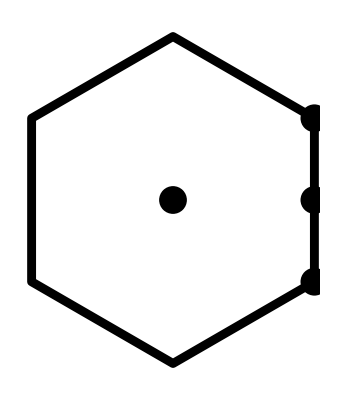

```mathematica
Scl=1.4;
Graphics[{Thickness[0.016],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]],PointSize[0.05],Point[{Γp,Kp,PauliMatrix[3].Kp,Mp}]}]
```

```mathematica
Export["BZ.pdf",%]
```

BZ.pdf

## For the legend I need:

```mathematica
Export["Region.bmp",HighSymPts]
```

Region.bmp

## Twisted bilayer graphene:

```mathematica
m=29;
r=7;
θ=-(ArcCos[(3 m^2+3m r+r^2/2)/(3 m^2+3m r+r^2)])*1.018;
θ0=30*2π/360;
θ//N

NAtoms=11;
NAtomsL=11;


Shiftz=0.4;
Shift={0,0,0};
PositionsCarbon=Join[Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1],Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1]];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

θ=-θ;

PositionsCarbon3=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)+{0,0,Shiftz}&/@PositionsCarbon;
Bonds31={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds1;
Bonds32={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds2;
Bonds33={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds3;
```

-0.126428

```mathematica
FULLLattice=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3,RCarb],Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds]},ImageSize->1200,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
ColorMoire=Green;
Color2=Gray;
Color3=Gray;
RadiusRegions=1;

MRLength=0.99/(2Sin[θ/2]);
a1=MRLength {Cos[π/6],Sin[π/6],0};
a2=MRLength{Cos[π/6],-Sin[π/6],0};
δ1=(a1+a2)/3;
δ2=2*(a1+a2)/3;

HighSymPts=Graphics3D[Join[{ColorMoire,Opacity[0.2],EdgeForm[None]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}},RadiusRegions],{n,{{0,0},{1,0},{0,1},{-1,0},{0,-1},{1,-1},{-1,1},{-2,0},{2,0}}}],{Color2,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ1,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ1},RadiusRegions],{n,{{0,0},{-1,-1},{-1,0},{-1,1},{0,-1},{1,-1},{1,0},{-2,0}}}],{Color3,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ2},RadiusRegions],{n,{{0,0},{0,-1},{0,-2},{-1,0},{-1,-1},{-2,0},{1,-1},{-2,-1}}}]],ViewPoint->{0,0,Infinity}];
```

```mathematica
Show[FULLLattice,HighSymPts,ImageSize->2000,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Export["TBG_Global.bmp",%]
```

TBG_Global.bmp

## Close up view for this system as well:

```mathematica
θ0=30*2π/360;
θ=-15.5*2π/360;
θ0=30*2π/360;

NAtoms=2;
NAtomsL=2;


Shiftz=0.4;
Shift={-1/√3,0,0};
PositionsCarbon=Join[Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1],Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1]];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

PositionsCarbon2=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,Shiftz}&/@PositionsCarbon;
Bonds21={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds1;
Bonds22={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds2;
Bonds23={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,Shiftz}}&/@Bonds3;
 
θ=-θ;

PositionsCarbon3=RotationMatrix[θ0+θ/2,{0,0,1}].(#+Shift)+{0,0,2Shiftz}&/@PositionsCarbon;
Bonds31={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds1;
Bonds32={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds2;
Bonds33={RotationMatrix[θ0+θ/2,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds3;

PositionsCarbon4=RotationMatrix[θ0+θ/2,{0,0,1}].#+{0,0,3Shiftz}&/@PositionsCarbon;
Bonds41={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds1;
Bonds42={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds2;
Bonds43={RotationMatrix[θ0+θ/2,{0,0,1}].#[[1]]+{0,0,3Shiftz},RotationMatrix[θ0+θ/2,{0,0,1}].#[[2]]+{0,0,3Shiftz}}&/@Bonds3;

CloseUpView=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3,RCarb],Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds]},ImageSize->1000,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
Export["TBGCloseUp.bmp",%]
```

TBGCloseUp.bmp

## Trilayer graphene on hBN:

```mathematica
m=29;
r=7;
θ0=30*2π/360;
Stretch=1.146;


NAtoms=12;
NAtomsL=12;


Shiftz=0.4;
Shift={0,0,0};

PositionsCarbonA=Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];PositionsCarbonB=Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon=Join[PositionsCarbonA,PositionsCarbonB];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;


PositionsCarbon3A=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonA;
PositionsCarbon3B=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonB;
Bonds31={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds1;
Bonds32={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds2;
Bonds33={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds3;
```

```mathematica
FULLLattice=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3A,RCarb],Orange,Sphere[PositionsCarbon3B,RCarb],Gray,Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds]},ImageSize->1200,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
ColorMoire=Green;
Color2=Gray;
Color3=Gray;
RadiusRegions=1;

MRLength=8.0
a1=MRLength {1,0,0};
a2=MRLength{Cos[π/3],Sin[π/3],0};
δ1=(a1+a2)/3;
δ2=2*(a1+a2)/3;

HighSymPts=Graphics3D[Join[{ColorMoire,Opacity[0.2],EdgeForm[None]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}},RadiusRegions],{n,{{0,0},{1,0},{0,1},{-1,0},{0,-1},{1,-1},{-1,1}}}],{Color2,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ1,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ1},RadiusRegions],{n,{{0,0},{-1,-1},{-1,0},{-1,1},{0,-1},{1,-1},{1,0},{-2,0}}}],{Color3,Opacity[0.1]},Table[Cylinder[{n[[1]]*a1+n[[2]]*a2+δ2,n[[1]]*a1+n[[2]]*a2+{0,0,0.1}+δ2},RadiusRegions],{n,{{0,0},{0,-1},{0,-2},{-1,0},{-1,-1},{-2,0},{1,-1},{-2,-1}}}]],ViewPoint->{0,0,Infinity}]
```

8.

-Graphics3D-

```mathematica
Show[FULLLattice,HighSymPts,ImageSize->2200,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
Export["TLG_Global.bmp",%]
```

TLG_Global.bmp

## Just to check the symmetries, let’s add the other layers as well

```mathematica
m=29;
r=7;
θ0=30*2π/360;
Stretch=1.146;


NAtoms=11;
NAtomsL=11;


Shiftz=0.4;
Shift={0,0,0};

PositionsCarbonA=Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];PositionsCarbonB=Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon=Join[PositionsCarbonA,PositionsCarbonB];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

Shift={-1/√3,0,0};

PositionsCarbon1L2=RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,Shiftz}&/@PositionsCarbon;
BondsL21={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds1;
BondsL22={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds2;
BondsL23={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds3;

Shift={-2/√3,0,0};

PositionsCarbon1L3=RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,2Shiftz}&/@PositionsCarbon;
BondsL31={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds1;
BondsL32={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds2;
BondsL33={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds3;

Shift={0,0,0};

PositionsCarbon3A=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonA;
PositionsCarbon3B=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonB;
Bonds31={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds1;
Bonds32={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds2;
Bonds33={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds3;
```

```mathematica
FULLLattice=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],ColorCarb2,Specularity[White,5],Sphere[PositionsCarbon1L2,RCarb],Cylinder[BondsL21,RBonds],Cylinder[BondsL22,RBonds],Cylinder[BondsL23,RBonds],ColorCarb4,Specularity[White,5],Sphere[PositionsCarbon1L3,RCarb],Cylinder[BondsL31,RBonds],Cylinder[BondsL32,RBonds],Cylinder[BondsL33,RBonds],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3A,RCarb],Orange,Sphere[PositionsCarbon3B,RCarb],Gray,Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds]},ImageSize->1200,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
Show[FULLLattice,HighSymPts,ImageSize->1500,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

## Finally, let’s do a close-up view for this system as well:

```mathematica
m=29;
r=7;
θ0=30*2π/360;
Stretch=1.46;


NAtoms=2;
NAtomsL=2;


Shiftz=0.4;
Shift={0,0,0};

PositionsCarbonA=Flatten[Table[{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];PositionsCarbonB=Flatten[Table[{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon=Join[PositionsCarbonA,PositionsCarbonB];

CylOrient=  Join[Flatten[Table[{{0,ypos,zpos},{1,ypos,zpos}},{ypos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,0,zpos},{xpos,1,zpos}},{xpos,0,1},{zpos,0,1}],1],Flatten[Table[{{xpos,ypos,0},{xpos,ypos,1}},{xpos,0,1},{ypos,0,1}],1]];
Bonds1=Flatten[Table[{{(√3)/2(j1+j2),1/2 j2-1/2 j1,0},{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds2=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+1+j2),1/2 j2-1/2(j1+1),0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];
Bonds3=Flatten[Table[{{(√3)/2(j1+j2)+1/√3,1/2 j2-1/2 j1,0},{(√3)/2(j1+j2+1),1/2(j2+1)-1/2 j1,0}},{j1,-NAtomsL,NAtoms,1},{j2,-NAtomsL,NAtoms,1}],1];

PositionsCarbon1=RotationMatrix[θ0,{0,0,1}].(#+Shift)&/@PositionsCarbon;
Bonds11={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds1;
Bonds12={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds2;
Bonds13={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift),RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)}&/@Bonds3;

Shift={-1/√3,0,0};

PositionsCarbon1L2=RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,-Shiftz}&/@PositionsCarbon;
BondsL21={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds1;
BondsL22={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds2;
BondsL23={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,Shiftz}}&/@Bonds3;

Shift={-2/√3,0,0};

PositionsCarbon1L3=RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,2Shiftz}&/@PositionsCarbon;
BondsL31={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds1;
BondsL32={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds2;
BondsL33={RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,2Shiftz},RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,2Shiftz}}&/@Bonds3;

Shift={0,0,0};

PositionsCarbon3A=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonA;
PositionsCarbon3B=Stretch*RotationMatrix[θ0,{0,0,1}].(#+Shift)+{0,0,3Shiftz}&/@PositionsCarbonB;
Bonds31={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds1;
Bonds32={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds2;
Bonds33={Stretch*RotationMatrix[θ0,{0,0,1}].(#[[1]]+Shift)+{0,0,3Shiftz},Stretch*RotationMatrix[θ0,{0,0,1}].(#[[2]]+Shift)+{0,0,3Shiftz}}&/@Bonds3;
```

```mathematica
FULLLattice=Graphics3D[{ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1,RCarb],Cylinder[Bonds11,RBonds],Cylinder[Bonds12,RBonds],Cylinder[Bonds13,RBonds],Opacity[0.1],EdgeForm[],ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1L2,RCarb],Cylinder[BondsL21,RBonds],Cylinder[BondsL22,RBonds],Cylinder[BondsL23,RBonds],ColorCarb,Specularity[White,5],Sphere[PositionsCarbon1L3,RCarb],Cylinder[BondsL31,RBonds],Cylinder[BondsL32,RBonds],Cylinder[BondsL33,RBonds],Opacity[1],ColorCarb3,Specularity[White,5],Sphere[PositionsCarbon3A,RCarb],Orange,Sphere[PositionsCarbon3B,RCarb],Gray,Cylinder[Bonds31,RBonds],Cylinder[Bonds32,RBonds],Cylinder[Bonds33,RBonds]},ImageSize->1200,ViewPoint->{0,0,Infinity},Boxed->False]
```

-Graphics3D-

```mathematica
Export["TLG_CloseUp.bmp",%]
```

TLG_CloseUp.bmp